# Shitcoin Protocol

Didactic Cryptocoin design.

## Import packages

```mathematica
Needs["ProgressMapping`",FileNameJoin[{NotebookDirectory[],"ProgressMapping.wl"}]];
```

## Cryptography functions

### Description:

### Implementation:

```mathematica
EllipticCurveEvaluate[x_,a_,b_]:=√(x^3+a x + b);
EllipticCurvePointQ[{x_,y_},a_,b_,p_]:=Block[{lhs,rhs},
lhs = Mod[y^2,p];
rhs = Mod[x^3+a x + b,p];

lhs == rhs
];
EllipticCurveAdd[{px_,py_},{qx_,qy_}]:=Block[{m,rx,ry},
If[px == qx,Return[∞]];
m = (qy - py)/(qx - px);
rx = m^2-px-qx;
ry = m (px-rx)-py;
{rx,ry}
];
EllipticCurveAdd[{px_,py_},{qx_,qy_},p_]:=Block[{snum,sden,s,rx,ry},
If[px == qx || !CoprimeQ[qx - px,p],Return[∞]];

snum = Mod[qy - py,p];
sden = ModularInverse[qx - px,p];
s = Mod[snum*sden,p];
rx = Mod[s^2-px-qx,p];
ry = Mod[s (px-rx)-py,p];
{rx,ry}
];
EllipticCurveDouble[{px_,py_},a_]:=Block[{m,rx,ry},
m = (3 px^2+a)/(2py);
rx = m^2-2px;
ry = m (px-rx)-py;
{rx,ry}
];
EllipticCurveDouble[{px_,py_},a_,p_]:=Block[{snum,sden,s,rx,ry},
snum = Mod[3 px^2+a,p];
If[py == 0||!CoprimeQ[2py,p],Return[∞]];
sden = ModularInverse[2py,p];
s = Mod[snum*sden,p];
rx = Mod[s^2-2px,p];
ry = Mod[s (px-rx)-py,p];
{rx,ry}
];

ComputeCyclicGroup[G_,a_,p_]:=Block[{G2},
G2 = EllipticCurveDouble[G,a,p];
Prepend[NestWhileList[EllipticCurveAdd[G,#,p]&,G2,#=!=∞&],G]
];
MultiplicationPath[G_,a_,p_,k_]:=Block[{G2},
G2 = EllipticCurveDouble[G,a,p];
Prepend[NestList[EllipticCurveAdd[G,#,p]&,G2,k-2],G]
];
MultiplyBasePoint[G_,a_,p_,k_]:=Block[{kBinary,P},
kBinary = Drop[IntegerDigits[k,2],1];
P = G;
Do[
P = EllipticCurveDouble[P,a,p];
If[kBinary[[i]] ==1,P = EllipticCurveAdd[P,G,p]];
,
{i,1,Length[kBinary]}
];
Return[P];
];
MultiplyBasePointHex[{hexGx_,hexGy_},aHex_,pHex_,kHex_]:=Block[{Gx,Gy,k,Px,Py,a,p},
Gx = FromDigits[hexGx,16];
Gy = FromDigits[hexGy,16];
k = FromDigits[kHex,16];
a = FromDigits[aHex,16];
p = FromDigits[pHex,16];
{Px,Py} = MultiplyBasePoint[{Gx,Gy},a,p,k];
{ToHex[Px,64],ToHex[Py,64]}
];
```

### Example operations

```mathematica
k = 5;
a = 2;
p = 17;
```

```mathematica
G = {5,1};
```

```mathematica
G2 = EllipticCurveDouble[G,a,p]
```

{6,3}

```mathematica
G3 = EllipticCurveAdd[G,G2,p]
```

{10,6}

```mathematica
MultiplyBasePoint[G,a,p,10]
```

{7,11}

### Curves over the Reals Field

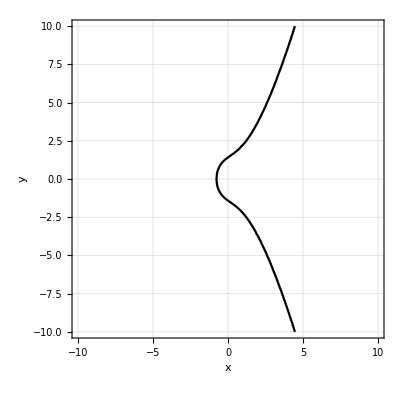

```mathematica
a = 2;
b = 2;
ContourPlot[y^2==x^3+a x + b,{x,-10,10},{y,-10,10},
PlotTheme->"Monochrome",
Frame->True,
BaseStyle->FontSize->14,
GridLines->Automatic,
FrameLabel->{Style["x",15],Style["y",15]}
]
```

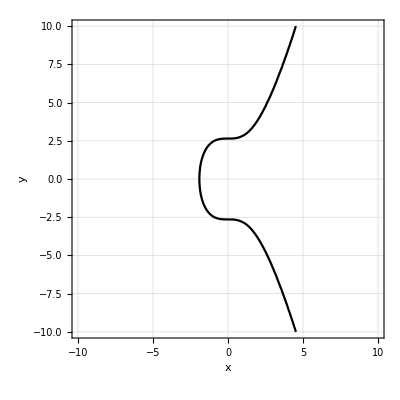

```mathematica
a = 0;
b = 7;
ContourPlot[y^2==x^3+a x + b,{x,-10,10},{y,-10,10},
PlotTheme->"Monochrome",
Frame->True,
BaseStyle->FontSize->14,
GridLines->Automatic,
FrameLabel->{Style["x",15],Style["y",15]}
]
```

```mathematica
G = {2,N@EllipticCurveEvaluate[2,a,b]}
```

{2,3.87298}

```mathematica
G2 = EllipticCurveDouble[G,a]
```

{-1.6,1.70411}

```mathematica
G3 = EllipticCurveAdd[G,G2]
```

{-0.037037,-2.64574}

```mathematica
G4 = EllipticCurveAdd[G,G3]
```

{8.27769,-23.9622}

```mathematica
G5= EllipticCurveAdd[G,G4]
```

{9.38258,28.8613}

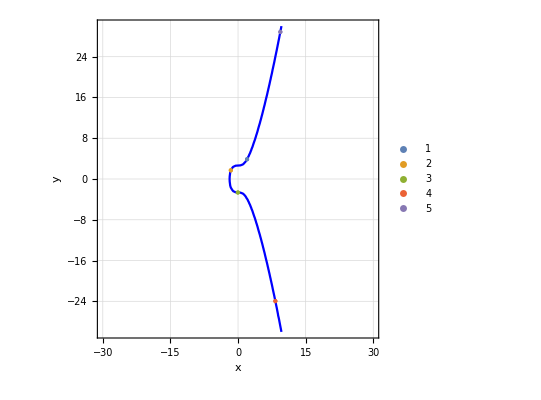

```mathematica
Show[
ContourPlot[y^2==x^3+a x + b,{x,-30,30},{y,-30,30},
PlotTheme->"Monochrome",
Frame->True,
BaseStyle->FontSize->14,
GridLines->Automatic,
FrameLabel->{Style["x",15],Style["y",15]},
ContourStyle->Blue
],
ListPlot[{{G},{G2},{G3},{G4},{G5}},
PlotStyle->PointSize[Large],
PlotLegends->Automatic
]
]
```

### Curves over Finite Field

```mathematica
CalculateCurvePoints[a_,b_,p_]:=Flatten[ProgressTable[If[EllipticCurvePointQ[{x,y},a,b,p],{x,y},Nothing],{x,0,p},{y,0,p}],1];
```

#### 𝔽_17

```mathematica
k = 5;
a = 2;
b = 2;
p = 17;
G = {5,1};
```

```mathematica
GGroup = ComputeCyclicGroup[G,a,p];
Thread[Range[Length[GGroup]]->GGroup]
```

{1→{5,1},2→{6,3},3→{10,6},4→{3,1},5→{9,16},6→{16,13},7→{0,6},8→{13,7},9→{7,6},10→{7,11},11→{13,10},12→{0,11},13→{16,4},14→{9,1},15→{3,16},16→{10,11},17→{6,14},18→{5,16},19→∞}

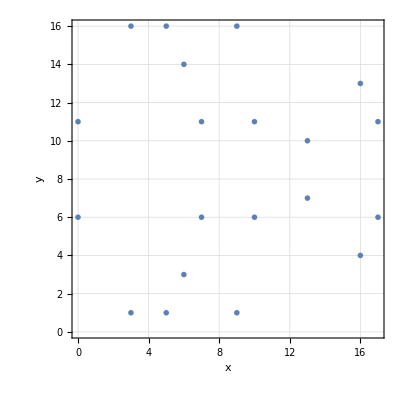

```mathematica
curveSet = CalculateCurvePoints[a,b,p];
ListPlot[curveSet,
AspectRatio->1,
PlotTheme->"Monochrome",
Frame->True,
BaseStyle->FontSize->14,
GridLines->Automatic,
FrameLabel->{Style["x",15],Style["y",15]}
]
```

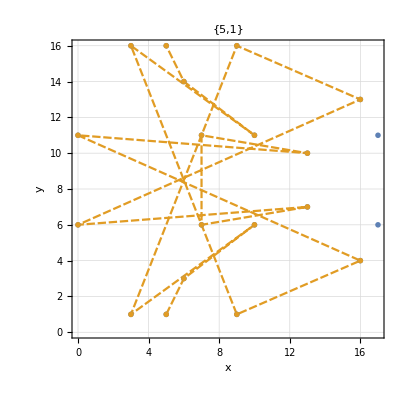

```mathematica
ListPlot[{curveSet,GGroup},
AspectRatio->1,
Joined->{False,True},
PlotTheme->"Monochrome",
Frame->True,
BaseStyle->FontSize->14,
GridLines->Automatic,
FrameLabel->{Style["x",15],Style["y",15]},
PlotLabel->"{5,1}"
]
```

#### 𝔽_421

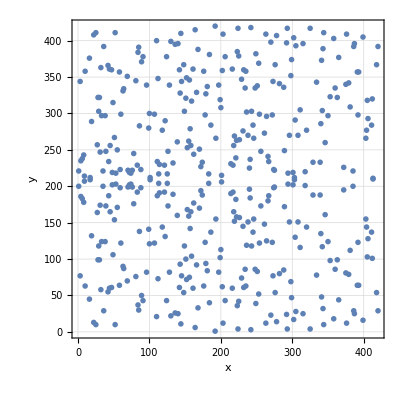

```mathematica
p = 421;
curveSet = CalculateCurvePoints[a,b,p];
ListPlot[curveSet,
AspectRatio->1,
PlotTheme->"Monochrome",
Frame->True,
BaseStyle->FontSize->14,
GridLines->Automatic,
FrameLabel->{Style["x",15],Style["y",15]}
]
```

```mathematica
GGroup = ComputeCyclicGroup[{6,183},a,p];
```

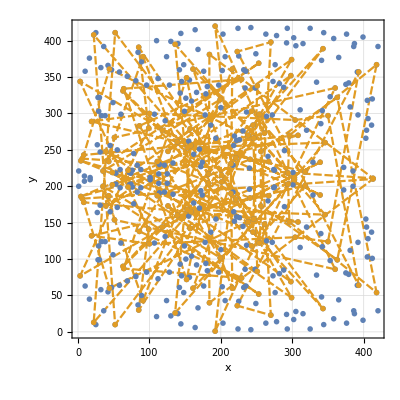

```mathematica
ListPlot[{curveSet,GGroup},
AspectRatio->1,
Joined->{False,True},
PlotTheme->"Monochrome",
Frame->True,
BaseStyle->FontSize->14,
GridLines->Automatic,
FrameLabel->{Style["x",15],Style["y",15]}
]
```

## ECDSA signature and verification

### Desciption:

### Implementation:

```mathematica
ECDSASign[G_,a_,p_,m_,k_,hash_,privateKey_]:=Block[{x,y,r,s},
{x,y} = MultiplyBasePoint[G,a,p,k];
r = x;
s = Mod[ModularInverse[k,m]*(hash+r*privateKey),m];
{r,s}
];
ECDSASignHex[{hexGx_,hexGy_},aHex_,pHex_,mHex_,kHex_,hashHex_,privateKeyHex_]:=Block[{Gx,Gy,a,p,m,k,hash,privateKey,r,s},
Gx = FromDigits[hexGx,16];
Gy = FromDigits[hexGy,16];
a = FromDigits[aHex,16];
p = FromDigits[pHex,16];
m = FromDigits[mHex,16];
k = FromDigits[kHex,16];
hash = FromDigits[hashHex,16];
privateKey = FromDigits[privateKeyHex,16];
{r,s} = ECDSASign[{Gx,Gy},a,p,m,k,hash,privateKey];

ToHex[r,64]<>ToHex[s,64]
];
ECDSAValidate[G_,a_,p_,m_,{r_,s_},hash_,publicKey_]:=Block[{w,u1,u2,X},
If[r<1 || r>m-1,Return[False]];
If[s<1 || s>m-1,Return[False]];

w = ModularInverse[s,m];
u1 = Mod[hash*w,m];
u2 = Mod[r*w,m];
X = EllipticCurveAdd[MultiplyBasePoint[G,a,p,u1],MultiplyBasePoint[publicKey,a,p,u2],p];
Mod[First[X],m] == r
];
ECDSAValidateHex[{hexGx_,hexGy_},aHex_,pHex_,mHex_,signature_,hashHex_,{publicKeyXHex_,publicKeyYHex_}]:=Block[{rHex,sHex,Gx,Gy,a,p,m,r,s,hash,publicKeyX,publicKeyY},
{rHex,sHex} = StringPartition[signature,64];
Gx = FromDigits[hexGx,16];
Gy = FromDigits[hexGy,16];
a = FromDigits[aHex,16];
p = FromDigits[pHex,16];
m = FromDigits[mHex,16];
r = FromDigits[rHex,16];
s = FromDigits[sHex,16];
hash = FromDigits[hashHex,16];
publicKeyX = FromDigits[publicKeyXHex,16];
publicKeyY = FromDigits[publicKeyYHex,16];

ECDSAValidate[{Gx,Gy},a,p,m,{r,s},hash,{publicKeyX,publicKeyY}]
];
```

#### Example:

```mathematica
a = 1;
b = 4;
p = 23;
G = {0,2};
m = Length[ComputeCyclicGroup[G,a,p]];
```

```mathematica
privateKey = 5
```

5

```mathematica
publicKey = MultiplyBasePoint[G,a,p,privateKey]
```

{7,20}

```mathematica
messageHash = 17;
```

```mathematica
{r,s} = ECDSASign[G,a,p,m,k,messageHash,privateKey]
```

{18,11}

```mathematica
ECDSAValidate[G,a,p,m,{r,s},messageHash,publicKey]
```

True

#### Visualization:

```mathematica
path = MultiplicationPath[G,a,p,privateKey]
```

{{0,2},{13,12},{11,9},{1,12},{7,20}}

```mathematica
curveSet = CalculateCurvePoints[a,b,p];
```

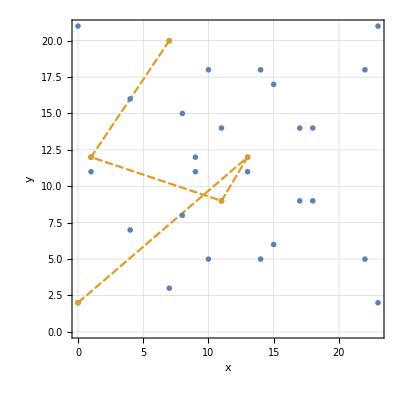

```mathematica
ListPlot[{curveSet,path},
AspectRatio->1,
Joined->{False,True},
PlotTheme->"Monochrome",
Frame->True,
BaseStyle->FontSize->14,
GridLines->Automatic,
FrameLabel->{Style["x",15],Style["y",15]}
]
```

## Network simulation

secp256k1 parameters

```mathematica
p = "FFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFEFFFFFC2F";
m = "FFFFFFFFFFFFFFFFFFFFFFFFFFFFFFFEBAAEDCE6AF48A03BBFD25E8CD0364141";
a = "0000000000000000000000000000000000000000000000000000000000000000";
b = "0000000000000000000000000000000000000000000000000000000000000007";
G = { "79BE667EF9DCBBAC55A06295CE870B07029BFCDB2DCE28D959F2815B16F81798","483ADA7726A3C4655DA4FBFC0E1108A8FD17B448A68554199C47D08FFB10D4B8"};
```

```mathematica
ToHex[n_,pad_ :64]:=IntegerString[n,16,pad];
Concatenate[l_]:=Apply[Join,l];
GenerateNodes[G_,a_,m_,n_]:=Block[{mdec,privateKeys,publicKeys,privateKeysPadded,publicKeysPadded},
mdec = FromDigits[m,16];
privateKeys = Table[ToHex[RandomInteger[{2,mdec-1}],64],n];
publicKeys = Map[StringJoin[MultiplyBasePointHex[G,a,m,#]]&,privateKeys];

MapThread[<|"PublicKey"->#1,"PrivateKey"->#2|>&,{publicKeys,privateKeys}]
];
```

```mathematica
networkNodes = GenerateNodes[G,a,p,10]
```

{<|PublicKey→936864b882a618a25708fd32e3287cac10d289a27b22cd130d3042e8e25e05cf74ea37cdd13550a4c2ce42c6d0e222d3410c4a00ddd932261e8e3b8ccd65a68f,PrivateKey→39629ecaccd9f717c1f515f7415f5d13ca2468be1de6c6966ce21f3af4c8029f|>,<|PublicKey→61249a16b3f56e3db642e5ca162beb0b64c3bee9e8768902c1482f6580e25de7a26590bb8cb37bbb4eb1fdc9a49d3e645a5ca480101030c732609033ccbc2b8b,PrivateKey→1946334d1e5cd7bb60a83ee3b6170eab392be71a862d56e5c7ef72a4db647101|>,<|PublicKey→5e6ac138d7041676c8cceaf562f5de44071aeddf90cf18e393b4288efdb8bb08048a73fee8baf07e577fd2d99588749360dd0c46ad953967cf6775232a0ea8be,PrivateKey→05dd2f218f631dafc92c8e8042501a9084de22a8495030f32012c695ee78fe76|>,<|PublicKey→8eb2357242224513080b264505b3a68d4db1dc36e1cfe0a50f0bd90a03f81de9376940dac7b6e6092ce7d54250b70e6b5282f605a9a81803005f2703c8734ed2,PrivateKey→401d188c38232c4612c94312684d1b5627ab22bd2f29279f86565d41c00608a0|>,<|PublicKey→8fdefc4cf847de6659a79c1641fa801aef8310b7b493cd5c810b4c3b5d58a99f43a298d156d9b71ee7b4584c5c79e89dace77d4b96d1e6634c9fcdcd289b2b0c,PrivateKey→9fda40e27f6d01d9b428d9467621ee76970478c4582fc27d0ed89561a0ff82cd|>,<|PublicKey→dded0656896dbaef475215738f5120b0f477c8f3110a65f5b30dedcb684ce600987642476c187fb88bef702061cb2a5aa78426f92397d4b59f290de923dd1ddc,PrivateKey→bf5fda59b79d949beb61d292235de6288b733bd2bd6b0856e76e992e24568b3f|>,<|PublicKey→24203ad958810688c6690f64b2ab410aa246b2fc00cd26565ac503604562e87173227191b2b54eb2abf86bd0711e77ffb74f7d371531f8b121e54e7ad3591569,PrivateKey→be8e3c235f19007081120a6f697ca8db0fb6eeb1e85996c775b797f6a784f7df|>,<|PublicKey→9bcfa371088022e83287d55892844fb08284bb5e402123e1bc608c7ab4dbf664cab4065c5bec6a127fb6ce11c3a8424f038aeff5a799a6b725362eb23e2459d2,PrivateKey→63a9b4f9f1c7550b233d9734aa38a7c3000f0970cf38b49820698bdcccc4330a|>,<|PublicKey→94698ebc7e686035d1cf40c503e15622bb4a0d9c82d7a2e40a09e3a5e69327a9e8fd48281d666dcde31652a9392fae483b02b620ae9ea634f8151bbb3428f42b,PrivateKey→f983987749daa34f40f20be9e8c30dd58916760ee8eab3934589f1389d326ee0|>,<|PublicKey→6798e006757a961c3394d90c1b1ab8fedce2ab563b68d8d17f65a729fa9aae25433e4d34f661f30e5206af049e154aa6018470f707969dba926605cc14c5e4bd,PrivateKey→c91bf857ddc61c2fdb4c1934e2a9ef4797f652f907a3b79ea4da204b935575fd|>}

```mathematica
Transaction[sender_,receiver_,units_]:=<|"Sender"->sender,"Receiver"->receiver,"Units"->units|>;
SimulateTransactions[networkNodes_,n_]:=Block[{transactors},
transactors = Take[Partition[RandomSample[networkNodes[[All,"PublicKey"]]],2],n];
Map[Transaction[First[#],Last[#],ToHex[RandomInteger[{1,255}],2]]&,transactors]
];

TransactionBlock[transactions_,prevBlockSignature_]:=prevBlockSignature<>StringJoin[Concatenate[Map[Values,transactions]]];
RandomNonceHex[m_]:=IntegerString[RandomInteger[{1,FromDigits[m,16]}],16];

MineBlock[G_,a_,p_,m_,hash_,privateKey_,difficulty_ : 2]:=Block[{i,signature,leadingDigits},
i = 1;
signature = "11";
leadingDigits = StringJoin[ConstantArray["0",difficulty]];

While[StringTake[signature,2] ≠ leadingDigits,
signature = ECDSASignHex[G,a,p,m,RandomNonceHex[m],hash,privateKey];
i++;
];
{i,signature}
];
```

```mathematica
transactions = SimulateTransactions[networkNodes,3]
```

{<|Sender→94698ebc7e686035d1cf40c503e15622bb4a0d9c82d7a2e40a09e3a5e69327a9e8fd48281d666dcde31652a9392fae483b02b620ae9ea634f8151bbb3428f42b,Receiver→8eb2357242224513080b264505b3a68d4db1dc36e1cfe0a50f0bd90a03f81de9376940dac7b6e6092ce7d54250b70e6b5282f605a9a81803005f2703c8734ed2,Units→6d|>,<|Sender→5e6ac138d7041676c8cceaf562f5de44071aeddf90cf18e393b4288efdb8bb08048a73fee8baf07e577fd2d99588749360dd0c46ad953967cf6775232a0ea8be,Receiver→dded0656896dbaef475215738f5120b0f477c8f3110a65f5b30dedcb684ce600987642476c187fb88bef702061cb2a5aa78426f92397d4b59f290de923dd1ddc,Units→e0|>,<|Sender→9bcfa371088022e83287d55892844fb08284bb5e402123e1bc608c7ab4dbf664cab4065c5bec6a127fb6ce11c3a8424f038aeff5a799a6b725362eb23e2459d2,Receiver→61249a16b3f56e3db642e5ca162beb0b64c3bee9e8768902c1482f6580e25de7a26590bb8cb37bbb4eb1fdc9a49d3e645a5ca480101030c732609033ccbc2b8b,Units→0d|>}

```mathematica
block = TransactionBlock[transactions,ToHex[0,128]]
```

0000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000094698ebc7e686035d1cf40c503e15622bb4a0d9c82d7a2e40a09e3a5e69327a9e8fd48281d666dcde31652a9392fae483b02b620ae9ea634f8151bbb3428f42b8eb2357242224513080b264505b3a68d4db1dc36e1cfe0a50f0bd90a03f81de9376940dac7b6e6092ce7d54250b70e6b5282f605a9a81803005f2703c8734ed26d5e6ac138d7041676c8cceaf562f5de44071aeddf90cf18e393b4288efdb8bb08048a73fee8baf07e577fd2d99588749360dd0c46ad953967cf6775232a0ea8bedded0656896dbaef475215738f5120b0f477c8f3110a65f5b30dedcb684ce600987642476c187fb88bef702061cb2a5aa78426f92397d4b59f290de923dd1ddce09bcfa371088022e83287d55892844fb08284bb5e402123e1bc608c7ab4dbf664cab4065c5bec6a127fb6ce11c3a8424f038aeff5a799a6b725362eb23e2459d261249a16b3f56e3db642e5ca162beb0b64c3bee9e8768902c1482f6580e25de7a26590bb8cb37bbb4eb1fdc9a49d3e645a5ca480101030c732609033ccbc2b8b0d

```mathematica
hash = Hash[block,"SHA256","HexString"]
```

2d61c71a084e1f019be8695470bd70e17da372ae80df9b3ffc247560923c7531

Simulation of nodes

```mathematica
AddRewardToBlock[transactions_,publicKey_]:=Append[transactions,<|"Sender"->ToHex[0,128],"Receiver"->publicKey,"Units"->"01"|>];
SimulateNode[prevBlockSignature_,transactions_,privateKey_,publicKey_,{G_,a_,p_,m_}]:=Block[{transactionsWithReward,block,hash,publicKeyParts},
transactionsWithReward = AddRewardToBlock[RandomSample[transactions],publicKey];
block = TransactionBlock[transactionsWithReward,prevBlockSignature];
hash = Hash[block,"SHA256","HexString"];
publicKeyParts = StringPartition[publicKey,64];

{block,publicKeyParts,MineBlock[G,a,p,m,hash,privateKey,2]}
];
```

```mathematica
nodesSimulation = ProgressMap[SimulateNode[ToHex[0,128],transactions,#["PrivateKey"],#["PublicKey"],{G,a,p,m}]&,networkNodes];
```

```mathematica
firstMine = First[MinimalBy[nodesSimulation[[All,3]],First]];
```

```mathematica
firstMiner  = FirstCase[nodesSimulation,{_,_,firstMine}];
```

```mathematica
newBlock = <|"TransactionBlock"->First[firstMiner],"Signature"->Last[Last[firstMiner]],"PublicKey"->firstMiner[[2]]|>
```

<|TransactionBlock→000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000009bcfa371088022e83287d55892844fb08284bb5e402123e1bc608c7ab4dbf664cab4065c5bec6a127fb6ce11c3a8424f038aeff5a799a6b725362eb23e2459d261249a16b3f56e3db642e5ca162beb0b64c3bee9e8768902c1482f6580e25de7a26590bb8cb37bbb4eb1fdc9a49d3e645a5ca480101030c732609033ccbc2b8b0d5e6ac138d7041676c8cceaf562f5de44071aeddf90cf18e393b4288efdb8bb08048a73fee8baf07e577fd2d99588749360dd0c46ad953967cf6775232a0ea8bedded0656896dbaef475215738f5120b0f477c8f3110a65f5b30dedcb684ce600987642476c187fb88bef702061cb2a5aa78426f92397d4b59f290de923dd1ddce094698ebc7e686035d1cf40c503e15622bb4a0d9c82d7a2e40a09e3a5e69327a9e8fd48281d666dcde31652a9392fae483b02b620ae9ea634f8151bbb3428f42b8eb2357242224513080b264505b3a68d4db1dc36e1cfe0a50f0bd90a03f81de9376940dac7b6e6092ce7d54250b70e6b5282f605a9a81803005f2703c8734ed26d000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000008eb2357242224513080b264505b3a68d4db1dc36e1cfe0a50f0bd90a03f81de9376940dac7b6e6092ce7d54250b70e6b5282f605a9a81803005f2703c8734ed201,Signature→007d7f5ee6e52b4f41d9d5229ec38ddf971db0af00a3c9c46c3115a90378f60ee9d2ee31e60358967b6fa21a19f7069a5b28dec501d1fc42a7cdf69d98f770b9,PublicKey→{8eb2357242224513080b264505b3a68d4db1dc36e1cfe0a50f0bd90a03f81de9,376940dac7b6e6092ce7d54250b70e6b5282f605a9a81803005f2703c8734ed2}|>

```mathematica
hash = Hash[newBlock["TransactionBlock"],"SHA256","HexString"];
signature = newBlock["Signature"];
publicKey = newBlock["PublicKey"];
```

```mathematica
ECDSAValidateHex[G,a,p,m,signature,hash,publicKey]
```

True

#### Iteration 2

```mathematica
transactions = SimulateTransactions[networkNodes,3]
```

{<|Sender→8fdefc4cf847de6659a79c1641fa801aef8310b7b493cd5c810b4c3b5d58a99f43a298d156d9b71ee7b4584c5c79e89dace77d4b96d1e6634c9fcdcd289b2b0c,Receiver→936864b882a618a25708fd32e3287cac10d289a27b22cd130d3042e8e25e05cf74ea37cdd13550a4c2ce42c6d0e222d3410c4a00ddd932261e8e3b8ccd65a68f,Units→ee|>,<|Sender→6798e006757a961c3394d90c1b1ab8fedce2ab563b68d8d17f65a729fa9aae25433e4d34f661f30e5206af049e154aa6018470f707969dba926605cc14c5e4bd,Receiver→61249a16b3f56e3db642e5ca162beb0b64c3bee9e8768902c1482f6580e25de7a26590bb8cb37bbb4eb1fdc9a49d3e645a5ca480101030c732609033ccbc2b8b,Units→69|>,<|Sender→dded0656896dbaef475215738f5120b0f477c8f3110a65f5b30dedcb684ce600987642476c187fb88bef702061cb2a5aa78426f92397d4b59f290de923dd1ddc,Receiver→5e6ac138d7041676c8cceaf562f5de44071aeddf90cf18e393b4288efdb8bb08048a73fee8baf07e577fd2d99588749360dd0c46ad953967cf6775232a0ea8be,Units→3a|>}

```mathematica
prevBlockSignature = newBlock["Signature"];
```

```mathematica
nodesSimulation = ProgressMap[SimulateNode[prevBlockSignature,transactions,#["PrivateKey"],#["PublicKey"],{G,a,p,m}]&,networkNodes];
```

```mathematica
firstMine = First[MinimalBy[nodesSimulation[[All,3]],First]];
firstMiner  = FirstCase[nodesSimulation,{_,_,firstMine}];
newBlock2 = <|"TransactionBlock"->First[firstMiner],"Signature"->Last[Last[firstMiner]],"PublicKey"->firstMiner[[2]]|>
```

<|TransactionBlock→007d7f5ee6e52b4f41d9d5229ec38ddf971db0af00a3c9c46c3115a90378f60ee9d2ee31e60358967b6fa21a19f7069a5b28dec501d1fc42a7cdf69d98f770b9dded0656896dbaef475215738f5120b0f477c8f3110a65f5b30dedcb684ce600987642476c187fb88bef702061cb2a5aa78426f92397d4b59f290de923dd1ddc5e6ac138d7041676c8cceaf562f5de44071aeddf90cf18e393b4288efdb8bb08048a73fee8baf07e577fd2d99588749360dd0c46ad953967cf6775232a0ea8be3a6798e006757a961c3394d90c1b1ab8fedce2ab563b68d8d17f65a729fa9aae25433e4d34f661f30e5206af049e154aa6018470f707969dba926605cc14c5e4bd61249a16b3f56e3db642e5ca162beb0b64c3bee9e8768902c1482f6580e25de7a26590bb8cb37bbb4eb1fdc9a49d3e645a5ca480101030c732609033ccbc2b8b698fdefc4cf847de6659a79c1641fa801aef8310b7b493cd5c810b4c3b5d58a99f43a298d156d9b71ee7b4584c5c79e89dace77d4b96d1e6634c9fcdcd289b2b0c936864b882a618a25708fd32e3287cac10d289a27b22cd130d3042e8e25e05cf74ea37cdd13550a4c2ce42c6d0e222d3410c4a00ddd932261e8e3b8ccd65a68fee000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000008eb2357242224513080b264505b3a68d4db1dc36e1cfe0a50f0bd90a03f81de9376940dac7b6e6092ce7d54250b70e6b5282f605a9a81803005f2703c8734ed201,Signature→00ade813fa79a3f34805c227c02df4b7ce02e8854b64c084735a1073cde85f99542cbdc161e9e14305ec2e172b7fbdde80e48fc9de6cfe62b0e98112972408cd,PublicKey→{8eb2357242224513080b264505b3a68d4db1dc36e1cfe0a50f0bd90a03f81de9,376940dac7b6e6092ce7d54250b70e6b5282f605a9a81803005f2703c8734ed2}|>

#### Iteration 3

```mathematica
transactions = SimulateTransactions[networkNodes,3]
```

{<|Sender→8fdefc4cf847de6659a79c1641fa801aef8310b7b493cd5c810b4c3b5d58a99f43a298d156d9b71ee7b4584c5c79e89dace77d4b96d1e6634c9fcdcd289b2b0c,Receiver→61249a16b3f56e3db642e5ca162beb0b64c3bee9e8768902c1482f6580e25de7a26590bb8cb37bbb4eb1fdc9a49d3e645a5ca480101030c732609033ccbc2b8b,Units→de|>,<|Sender→936864b882a618a25708fd32e3287cac10d289a27b22cd130d3042e8e25e05cf74ea37cdd13550a4c2ce42c6d0e222d3410c4a00ddd932261e8e3b8ccd65a68f,Receiver→24203ad958810688c6690f64b2ab410aa246b2fc00cd26565ac503604562e87173227191b2b54eb2abf86bd0711e77ffb74f7d371531f8b121e54e7ad3591569,Units→08|>,<|Sender→9bcfa371088022e83287d55892844fb08284bb5e402123e1bc608c7ab4dbf664cab4065c5bec6a127fb6ce11c3a8424f038aeff5a799a6b725362eb23e2459d2,Receiver→8eb2357242224513080b264505b3a68d4db1dc36e1cfe0a50f0bd90a03f81de9376940dac7b6e6092ce7d54250b70e6b5282f605a9a81803005f2703c8734ed2,Units→f0|>}

```mathematica
prevBlockSignature = newBlock2["Signature"];
```

```mathematica
nodesSimulation = ProgressMap[SimulateNode[prevBlockSignature,transactions,#["PrivateKey"],#["PublicKey"],{G,a,p,m}]&,networkNodes];
```

```mathematica
firstMine = First[MinimalBy[nodesSimulation[[All,3]],First]];
firstMiner  = FirstCase[nodesSimulation,{_,_,firstMine}];
newBlock3 = <|"TransactionBlock"->First[firstMiner],"Signature"->Last[Last[firstMiner]],"PublicKey"->firstMiner[[2]]|>
```

<|TransactionBlock→00ade813fa79a3f34805c227c02df4b7ce02e8854b64c084735a1073cde85f99542cbdc161e9e14305ec2e172b7fbdde80e48fc9de6cfe62b0e98112972408cd8fdefc4cf847de6659a79c1641fa801aef8310b7b493cd5c810b4c3b5d58a99f43a298d156d9b71ee7b4584c5c79e89dace77d4b96d1e6634c9fcdcd289b2b0c61249a16b3f56e3db642e5ca162beb0b64c3bee9e8768902c1482f6580e25de7a26590bb8cb37bbb4eb1fdc9a49d3e645a5ca480101030c732609033ccbc2b8bde9bcfa371088022e83287d55892844fb08284bb5e402123e1bc608c7ab4dbf664cab4065c5bec6a127fb6ce11c3a8424f038aeff5a799a6b725362eb23e2459d28eb2357242224513080b264505b3a68d4db1dc36e1cfe0a50f0bd90a03f81de9376940dac7b6e6092ce7d54250b70e6b5282f605a9a81803005f2703c8734ed2f0936864b882a618a25708fd32e3287cac10d289a27b22cd130d3042e8e25e05cf74ea37cdd13550a4c2ce42c6d0e222d3410c4a00ddd932261e8e3b8ccd65a68f24203ad958810688c6690f64b2ab410aa246b2fc00cd26565ac503604562e87173227191b2b54eb2abf86bd0711e77ffb74f7d371531f8b121e54e7ad35915690800000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000000dded0656896dbaef475215738f5120b0f477c8f3110a65f5b30dedcb684ce600987642476c187fb88bef702061cb2a5aa78426f92397d4b59f290de923dd1ddc01,Signature→008bc9d3eee592ea92a36266258f39cf9a56e8b42b803685c93432738bce647d6123d9eb5d39c24eae1b7b1877e859d39e22fbbef67e37a3289dad0c6d3a0c72,PublicKey→{dded0656896dbaef475215738f5120b0f477c8f3110a65f5b30dedcb684ce600,987642476c187fb88bef702061cb2a5aa78426f92397d4b59f290de923dd1ddc}|>

### 8 random trials

```mathematica
hash = Hash[block,"SHA256","HexString"]
```

a397a3076b6d92b723348b671be686c6d8fbcd19757ca8cda5fc272445895fad

```mathematica
signatures = Table[ECDSASignHex[G,a,p,m,ToHex[k,64],hash,privateKey],{k,2,10}]
```

{c6047f9441ed7d6d3045406e95c07cd85c778e4b8cef3ca7abac09b95c709ee5530ba3f44d230db31a114b9fac405628476fc487ab8812324438d4933af238ea,f9308a019258c31049344f85f89d5229b531c845836f99b08601f113bce036f93850de47cb04a677d8db98acc82ecbef9402650f7278813b4bd5c8e7cf45e3a8,e493dbf1c10d80f3581e4904930b1404cc6c13900ee0758474fa94abe8c4cd13d0add5c9d2a78639972ee30b87758c09adee21d48e2b425d6710acf835221d19,2f8bde4d1a07209355b4a7250a5c5128e88b84bddc619ab7cba8d569b240efe46d7b6e78ebeb0059caf45c42358fa715c7cf400bd8cef5949b7f125da76ca298,fff97bd5755eeea420453a14355235d382f6472f8568a18b2f057a1460297556396502ce141a28bdfd8eb783dfca183ba8e999f8a13cff93cdc651679c8b8b85,5cbdf0646e5db4eaa398f365f2ea7a0e3d419b7e0330e39ce92bddedcac4f9bc6ff0117e33c9a8ebc2af7f681fb5e371f46a655d2441ab40078bacc9ac32e824,2f01e5e15cca351daff3843fb70f3c2f0a1bdd05e5af888a67784ef3e10a2a0125525e7381636ed50a5c55584595223489c34f469204dfa774c3652b7f2bd652,acd484e2f0c7f65309ad178a9f559abde09796974c57e714c35f110dfc27ccbe6d8b4aec4af971c5270fc158da2ef468f696d3c1bd6cdf471a9373d795e56afd,a0434d9e47f3c86235477c7b1ae6ae5d3442d49b1943c2b752a68e2a47e247c7c26d422b5b092c50792f36e3cf15db61781483957a206f90179c09c5c5ce42ba}